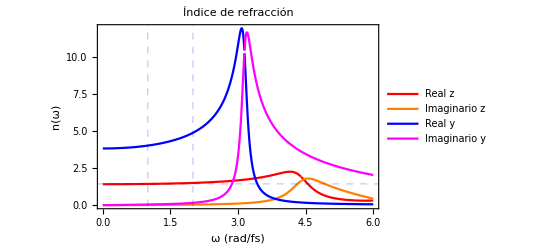

Índice de refracción wz

1.43296

Índice de refracción wy

4.88482

Ajuste de fase (1/μm)

-23.0285

Longitud de coherencia (μm)

-0.136422

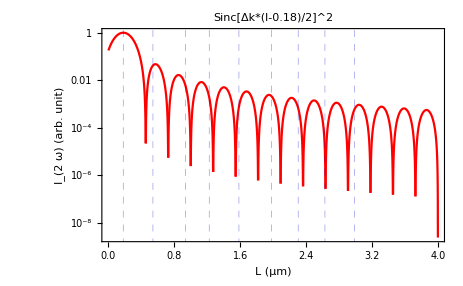

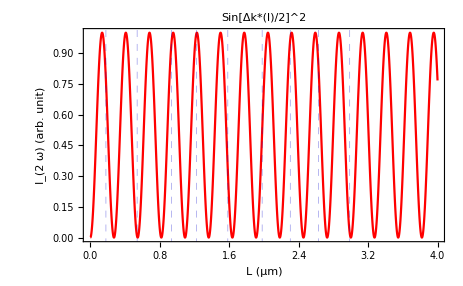

```mathematica
wpulsoz=1;(*rad/fs*)(*Puslo láser*)
wpulsoz=wpulsoz/wpulsoz ; 
wpulsoy=2*wpulsoz; (*rad/fs*)(*Queremos generar el segundo armónico*)(*Ver luego el espectro generado con la TF*)
(*-----------------------------------Resonancia del medio dispersivo en z--------------------------*)
f1z=0.7; (*Hz/fs*)
delta1z=0.5*f1z; (*Hz/fs*) (*Constante de amortiguamiento*)
w1z=2*Pi*f1z/wpulsoz; (*rad/fs*) (*Frecuencia de Resonancia*)
εsz=2;
εinfz=1;
G1z=1;
b1z=G1z*(εsz-εinfz);
εrz[w_]:=εinfz+((εsz-εinfz)*w1z^2)/(w1z^2-2*I*w*delta1z-w^2);
Plot[{Re[εrz[w]],Im[εrz[w]]},{w,0,200},PlotRange->All, PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1]}, Frame->True,FrameLabel->{"ω (rad/fs)","ε(ω)"," "," "},PlotLabel->Style["Permitividad Relativa",16,Black],FrameStyle->{Black,Black,Black,Black},PlotLegends->{"Real","Imaginaria"}];
(*-----------------------------------Resonancia del medio dispersivo en y--------------------------*)
f1y=0.5; (*Hz/fs*)
delta1y=0.2*f1y; (*Hz/fs*) (*Constante de amortiguamiento*)
w1y=2*Pi*f1y/wpulsoz; (*rad/fs*) (*Frecuencia de Resonancia*)
εsy=14.6289;
εinfy=1;
G1y=1;
b1y=G1y*(εsy-εinfy);
εry[w_]:=εinfy+((εsy-εinfy)*w1y^2)/(w1y^2-2*I*w*delta1y-w^2);
Plot[{Re[εry[w]],Im[εry[w]]},{w,0,200},PlotRange->All, PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1]}, Frame->True,FrameLabel->{"ω (rad/fs)","ε(ω)"," "," "},PlotLabel->Style["Permitividad Relativa",16,Black],FrameStyle->{Black,Black,Black,Black},PlotLegends->{"Real","Imaginaria"}];

Plot[{Re[Sqrt[εrz[w]]],Im[Sqrt[εrz[w]]],Re[Sqrt[εry[w]]],Im[Sqrt[εry[w]]]},{w,0,6},PlotRange->All, PlotStyle->{RGBColor[1,0,0],RGBColor[1,0.5,0],RGBColor[0,0,1],RGBColor[1,0,1]}, Frame->True,FrameLabel->{"ω (rad/fs)","n(ω)"," "," "},PlotLabel->Style["Índice de refracción",16,Black],FrameStyle->{Black,Black,Black,Black},PlotLegends->{"Real z","Imaginario z","Real y","Imaginario y"},GridLines->{{{wpulsoy/wpulsoz,Directive[RGBColor[0,0,0.8],Dashed,Thick]},{wpulsoz/wpulsoz,Directive[RGBColor[0,0,0.8],Dashed,Thick]}},{{n2z[wpulsoz],Directive[RGBColor[0,0,0.8],Dashed,Thick]}}}]
(*----------------Cálculo para wz-----------------------*)
n2z[w_]:=Abs[Sqrt[εrz[w]]]
"Índice de refracción wz"
n2z[wpulsoz]
(*----------------Cálculo para wy-----------------------*)
n2y[w_]:=Abs[Sqrt[εry[w]]]
"Índice de refracción wy"
n2y[wpulsoy]
(*----------------Cálculo Ajuste de fase-----------------------*)
c=2.9979*10^-1;(*micro m/fs*)
"Ajuste de fase (1/μm)"
Δk=(2*wpulsoz(n2z[wpulsoz]-n2y[wpulsoy]))/c
"Longitud de coherencia (μm)"
LC=Pi/Δk
LogPlot[{Sinc[Δk*(l-0.18)/2]^2},{l,0,4},PlotRange->All, PlotStyle->{RGBColor[1,0,0]}, Frame->True,FrameLabel->{"L (μm)","I_(2  ω) (arb. unit)"," "," "},PlotLabel->Style["Sinc[Δk*(l-0.18)/2]^2",16,Black],FrameStyle->{Black,Black,Black,Black},GridLines->{{{0.18,Directive[RGBColor[0,0,0.8],Dashed,Thick]},{0.54,Directive[RGBColor[0,0,0.8],Dashed,Thick]},{0.936,Directive[RGBColor[0,0,0.8],Dashed,Thick]},{1.224,Directive[RGBColor[0,0,0.8],Dashed,Thick]},{1.584,Directive[RGBColor[0,0,0.8],Dashed,Thick]},{1.98,Directive[RGBColor[0,0,0.8],Dashed,Thick]},{2.304,Directive[RGBColor[0,0,0.8],Dashed,Thick]},{2.628,Directive[RGBColor[0,0,0.8],Dashed,Thick]},{2.988,Directive[RGBColor[0,0,0.8],Dashed,Thick]}},None}]
Plot[{Sin[Δk*(l)/2]^2},{l,0,4},PlotRange->All, PlotStyle->{RGBColor[1,0,0]}, Frame->True,FrameLabel->{"L (μm)","I_(2  ω) (arb. unit)"," "," "},PlotLabel->Style["Sin[Δk*(l)/2]^2",16,Black],FrameStyle->{Black,Black,Black,Black},GridLines->{{{0.18,Directive[RGBColor[0,0,0.8],Dashed,Thick]},{0.54,Directive[RGBColor[0,0,0.8],Dashed,Thick]},{0.936,Directive[RGBColor[0,0,0.8],Dashed,Thick]},{1.224,Directive[RGBColor[0,0,0.8],Dashed,Thick]},{1.584,Directive[RGBColor[0,0,0.8],Dashed,Thick]},{1.98,Directive[RGBColor[0,0,0.8],Dashed,Thick]},{2.304,Directive[RGBColor[0,0,0.8],Dashed,Thick]},{2.628,Directive[RGBColor[0,0,0.8],Dashed,Thick]},{2.988,Directive[RGBColor[0,0,0.8],Dashed,Thick]}},None}]
```

```mathematica
"Cálculo de la eficiencia SHG"
L=4.644; (*micro m*)
intenw=1.3666*10^3;
e0=8.854*10^-12/10^6 ; (*F/ micro m*)
chi=10^10;
xi2=1/(4*e0*chi*intenw)
deff=0.5*xi2;
eficienciaSHG=L^2*(Sin[Δk*L/2]/(Δk*L/2))^2*intenw (*(8*wpulsoz1^2*deff^2)/(n2y[wpulsoy]*n2z[wpulsoz]^2*e0*c^2)*)
```